```mathematica
as=#>0&/@{ja,jw,jg,jr,Uah,Ual,Ubg,Uwh,Uwl,Uoh,Uol,Ugh,Ugl,TT,UU,QQ};
sheet[x_,p_,w_,g_]:=(Tanh[2(x-p+w/2)/g]-Tanh[2(x-p-w/2)/g])/2
```

### Choose FAC cut

```mathematica
j1[x_,c_,ja_,jw_,jg_,jr_]:=ja(sheet[x,c+jw/2,jw,jg]-sheet[x,c-jr jw/2,jr jw,jg]/jr)
FullSimplify[D[Normal[Series[j1[x,c,ja,jw,jg,jr],{x,#,1}]],x]/.jw->∞,Assumptions->as]&/@{c-jr jw,c,c+jw}
```

{-ja/(jg jr),(ja (1+jr))/(jg jr),-ja/jg}

### Choose potential drop cut

```mathematica
Ud[x_,c_,Uah_,Ual_,Ubg_,Uwh_,Uwl_,Uoh_,Uol_,Ugh_,Ugl_]:=(Uah-Ual)sheet[x,c+Uoh,Uwh,Ugh]+(Ual-Ubg)sheet[x,c+Uol,Uwl,Ugl]+Ubg
FullSimplify[D[Normal[Series[Ud[x,c,Uah,Ual,Ubg,Uwh,Uwl,Uoh,Uol,Ugh,Ugl],{x,#,1}]],x]/.Uwh->∞/.Uwl->∞,Assumptions->as]&/@{c+Uol-Uwl/2,c+Uol+Uwl/2,c+Uoh-Uwh/2,c+Uoh+Uwh/2}
```

{(Ual-Ubg)/Ugl,(-Ual+Ubg)/Ugl,(Uah-Ual)/Ugh,(-Uah+Ual)/Ugh}

### Calculate total precipitation based on Lyons-Evans-Lundin / field-aligned conductance, K

```mathematica
Jpar=Piecewise[{{QQ/(TT^2+(TT+UU)^2)EE/TT Exp[-(EE-UU)/TT],EE≥UU}},0];
jacc=FullSimplify[qq Integrate[Jpar,{EE,0,∞},Assumptions->as],Assumptions->as]
Q==Solve[jacc==KK(*A/V/m^2*)(TT+UU)(*eV*)/qq,QQ][[1,1,2]]
```

(qq QQ (TT+UU))/(2 TT^2+2 TT UU+UU^2)

Q==(KK (2 TT^2+2 TT UU+UU^2))/qq^2

### Determine source density

```mathematica
FullSimplify[Solve[KK==1/Sqrt[β] qq Ns Sqrt[1/(2π mm TT)],Ns][[1,1,2]],Assumptions->{TT>0,mm>0}](*see Morooka et al. (2004)*)
```

(KK √(2 π) √(mm TT β))/qq

```mathematica
vc=2.99792 10^8;(*m/s*)
qe=1.60218 10^-19;(*C*)
me=5.10999 10^5/vc^2;(*eV s^2/m^2*)
NS==KK Sqrt[2π me TT]/qe Sqrt[β](*m^-3*)
```

NS==3.73051×10^13 KK √TT √β

### Get average energy

```mathematica
FullSimplify[Integrate[EE Jpar,{EE,0,∞},Assumptions->as]/Integrate[Jpar,{EE,0,∞},Assumptions->as],Assumptions->as](*eV*)
```

TT+UU+TT^2/(TT+UU)

### Get magnetic field deviation

```mathematica
FullSimplify[Integrate[j1[x,c,a,w,g,r],x],Assumptions->{a>0,w>0,g>0,r>0}]
```

(a g ((1+r) Log[Cosh[(2 (c-x))/g]]-r Log[Cosh[(2 (c+w-x))/g]]-Log[Cosh[(2 (c-r w-x))/g]]))/(4 r)

### Plot

```mathematica
jscale=10^6;
Uscale=10^-3;
Qscale=10^3/10;
Escale=10^3/10;
Nscale=10^-6;
Manipulate[
jplot=j1[x,c,ja,jw,jg,jr];(*A/m^2*)
Uplot=Ud[x,c,Uah,Ual,Ubg,Uwh,Uwl,Uoh,Uol,Ugh,Ugl];(*eV*)
Qplot=Kpar(2 Ts^2+2 Ts Uplot+Uplot^2);(*W/m^2*)
Ns=3.73051 10^13 Kpar Sqrt[Ts];
jaccplot=Kpar(Uplot+Ts);(*A/m^2*)
Ebar=Ts+Uplot+Ts^2/(Ts+Uplot);(*eV*)
(*ΣP=Sqrt[((40Ebar/1000)/(16+(Ebar/1000)^2))^2 Qplot 1000+0(5.7)^2 Qplot 1000];(*A/V*)*)
ΣP=40(Ebar/1000)/(16+(Ebar/1000)^2)Sqrt[Qplot 1000];(*A/V*)
ΣPinf=ΣP/.x->-∞(*A/V*);
intj=(ja jg ((1+jr) Log[Cosh[(2 (c-x))/jg]]-jr Log[Cosh[(2 (c+jw-x))/jg]]-Log[Cosh[(2 (c-jr jw-x))/jg]]))/(4 jr);(*A/m*)
E3plot=Simplify[(intj+ΣPinf E3inf)/(γ ΣP+(1-γ)ΣPinf)];(*V/m*)
jplot=D[(ΣP E3plot)/.x->xx,xx]/.xx->x;(*A/m^2*)
Plot[{
-jplot jscale
,-(ja/2-(c ja)/jg-ja/(2 jr)-(c ja)/(jg jr)+(ja x)/jg+(ja x)/(jg jr))jscale
,-((ja jw)/jg+ja/2+(c ja)/jg-(ja x)/jg)jscale
,-(-((ja jw)/jg)-ja/(2 jr)+(c ja)/(jg jr)-(ja x)/(jg jr))jscale
,Uplot Uscale
,Qplot Qscale
,E3plot Escale
,-jaccplot jscale
},{x,-150000,250000}
,Frame->True
,FrameLabel->{{"",""},{"North (km)","N_S/β^(1/2) = "<>ToString[SetPrecision[Ns Nscale,2]]<>" cm^-3   Q_BG = "<>ToString[SetPrecision[10.^3 Qplot/.x->-∞,2]]<>" mW/m^2"}}
,FrameStyle->Directive[Black,20]
,LabelStyle->Directive[Black,20,"Arial"]
,PlotRange->{All,{-1,2}5}
,GridLines->{{
c-jw jr-jg/2
,c-jw jr+jg/2
,c+jg/2
,c-jg/2
,c+jw-jg/2
,c+jw+jg/2
},{ja/jr jscale,-ja jscale}}
,AspectRatio->0.6
,ImageSize->Full
,PlotStyle->{Red,{Red,Dashed,Opacity[0.1]},{Red,Dashed,Opacity[0.1]},{Red,Dashed,Opacity[0.1]},Blue,Darker@Green,Orange,{Red,Dashed},Magenta}
,PlotLegends->Placed[{"j_(||) (μA/m^2)",None,None,None,"U_(||) (keV)","Q (10 mW/m^2)","E_N (10 mV/m)","j_acc (μA/m^2)"},{Left,Top}]
]
,{{c,0},-400000,400000}
,{{ja,0.5 10^-6},0,10 10^-6}
,{{jw,200000},100000,300000}
,{{jr,0.3333},0.01,1}
,{{jg,20000},5000,50000}
,{{Ubg,100},0,2000}
,{{Ual,8000},1000,10000}
,{{Uah,8000},1000,10000}
,{{Uol, 70000},-400000,400000}
,{{Uoh,70000},-400000,400000}
,{{Uwl,100000},50000,400000}
,{{Uwh,20000},10000,50000}
,{{Ugl,40000},10000,100000}
,{{Ugh,5000},1000,10000}
,{{Kpar,1 10^-10},10^-12,10^-9}
,{{Ts,1000},0,10000}
,{{E3inf,0},-0.05,0.05}
,{{γ,1},0,1}
]
```

## GEMINI

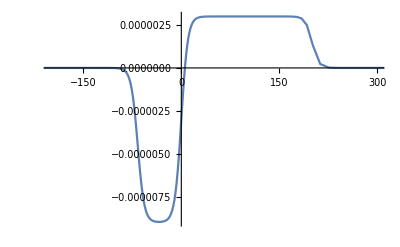

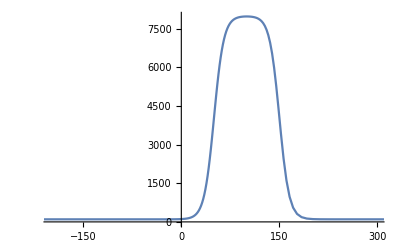

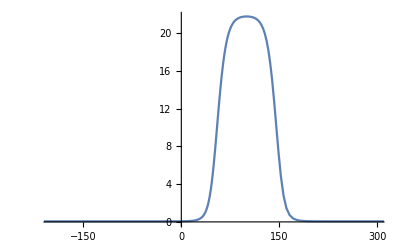

```mathematica
dir="D:\\Files\\research\\thesis\\runs\\aurora_null_03_2d";
time=35950;
x3=Import[dir<>"\\inputs\\simgrid.h5","/x3"][[3;;-3]]/1000;
gemj1=Import[dir<>"\\inputs\\fields\\20150201_"<>ToString[time]<>".000000.h5","Vmaxx1it"][[;;,1]];
gemUd=Import[dir<>"\\inputs\\particles\\20150201_"<>ToString[time]<>".000000.h5","/E0p"][[;;,1]];
gemQ0=Import[dir<>"\\inputs\\particles\\20150201_"<>ToString[time]<>".000000.h5","/Qp"][[;;,1]];
ListLinePlot[Transpose[{x3,gemj1}],PlotRange->{{-200,300},All}]
ListLinePlot[Transpose[{x3,gemUd}],PlotRange->{{-200,300},All}]
ListLinePlot[Transpose[{x3,gemQ0}],PlotRange->{{-200,300},All}]
```

```mathematica
gemne=Import[dir<>"\\20150201_"<>ToString[time]<>".000000.h5","nsall"][[7,;;,1,;;]];
gemj1all=Import[dir<>"\\20150201_"<>ToString[time]<>".000000.h5","J1all"][[;;,1,;;]] 10^6;
gemj2all=Import[dir<>"\\20150201_"<>ToString[time]<>".000000.h5","J2all"][[;;,1,;;]] 10^6;
gemj3all=Import[dir<>"\\20150201_"<>ToString[time]<>".000000.h5","J3all"][[;;,1,;;]] 10^6;
gemv2all=Import[dir<>"\\20150201_"<>ToString[time]<>".000000.h5","v2avgall"][[;;,1,;;]] 10^-3;
gemv3all=Import[dir<>"\\20150201_"<>ToString[time]<>".000000.h5","v3avgall"][[;;,1,;;]] 10^-3;
MatrixPlot[Reverse@Transpose@gemne,PlotLegends->Automatic]
MatrixPlot[Reverse@Transpose@gemj1all,PlotLegends->Automatic]
MatrixPlot[Reverse@Transpose@gemj2all,PlotLegends->Automatic]
MatrixPlot[Reverse@Transpose@gemj3all,PlotLegends->Automatic]
MatrixPlot[Reverse@Transpose@gemv2all,PlotLegends->Automatic]
MatrixPlot[Reverse@Transpose@gemv3all,PlotLegends->Automatic]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

# OLD

```mathematica
intj
```

-0.015 Log[Sech[0.0001 x]^2]+0.0025 Log[1.-1. Tanh[30.-0.0001 x]^2]+0.0125 Log[1.-1. Tanh[6.+0.0001 x]^2]

### Calculate total precipitation based on r_acc and T_s

```mathematica
phi=QQ/(Ts^2+(Ts+UU)^2)EE/Ts Exp[-(EE-UU)/Ts];
jacc=FullSimplify[qe Integrate[phi,{EE,UU,∞},Assumptions->as],Assumptions->as]
Solve[jacc==racc jj,QQ][[1,1,2]]
```

(qe QQ (Ts+UU))/(Ts^2+(Ts+UU)^2)

(jj racc (2 Ts^2+2 Ts UU+UU^2))/(qe (Ts+UU))

#### Side note: Knight: j_acc[x] goes as u[x] and, as t goes to u (Maxwellian), then q[x] goes as u[x]^2 (see Fridman & Lemaire)

```mathematica
Q[x_,c_,racc_,Ts_,ja_,Uah_,Ual_,Ubg_,Uwh_,Uwl_,Uoh_,Uol_,Ugh_,Ugl_]:=(racc ja(2 Ts^2+2 Ts UU+UU^2))/((*1.60218 10^-19*)(Ts+UU))/.UU->U[x,c,Uah,Ual,Ubg,Uwh,Uwl,Uoh,Uol,Ugh,Ugl](*W/m^2*)
```

```mathematica
(*Qother[x_,c_,racc_,ja_,jw_,jg_,jr_,Ts_,Uah_,Ual_,Ubg_,Uwh_,Uwl_,Uoh_,Uol_,Ugh_,Ugl_]:=(racc j[x,c,ja,jw,jg,jr] (2 Ts^2+2 Ts UU+UU^2))/((*1.60218 10^-19*)(Ts+UU))/.UU->U[x,c,Uah,Ual,Ubg,Uwh,Uwl,Uoh,Uol,Ugh,Ugl]*)
```

### Get the electric field

#### Get Pedersen conductance

```mathematica
Ebar=FullSimplify[Integrate[EE phi,{EE,UU,∞},Assumptions->as]/Integrate[phi,{EE,UU,∞},Assumptions->as],Assumptions->as](*eV*)
ΣP[Ebar_,Q_]:=Sqrt[((40Ebar/1000)/(16+(Ebar/1000)^2))^2 Q 1000+(5.7)^2 Q 1000]
```

Ts+UU+Ts^2/(Ts+UU)

```mathematica
ΣPx=ΣP[Ebar/.UU->U[x,c,Uah,Ual,Ubg,Uwh,Uwl,Uoh,Uol,Ugh,Ugl],Q[x,c,racc,Ts,ja,Uah,Ual,Ubg,Uwh,Uwl,Uoh,Uol,Ugh,Ugl]];
ΣPinf=ΣP[Ebar/.UU->Ubg,(racc ja(2 Ts^2+2 Ts Ubg+Ubg^2))/(Ts+Ubg)];
intj=Integrate[j[xx,cc,aa,ww,gg,rr],xx]
```

1/4 aa gg Log[Cosh[(2 (cc-xx))/gg]]+(aa gg Log[Cosh[(2 (cc-xx))/gg]])/(4 rr)-1/4 aa gg Log[Cosh[(2 (cc+ww-xx))/gg]]-(aa gg Log[Cosh[(2 (cc-rr ww-xx))/gg]])/(4 rr)

```mathematica
E3[x_,c_,racc_,Ts_,E3inf_,ja_,jw_,jg_,jr_,Uah_,Ual_,Ubg_,Uwh_,Uwl_,Uoh_,Uol_,Ugh_,Ugl_]:=(intj/.{xx->x,cc->c,aa->ja,ww->jw,gg->jg,rr->jr}+ΣP[Ebar/.UU->Ubg,(racc ja(2 Ts^2+2 Ts Ubg+Ubg^2))/(Ts+Ubg)] E3inf)/ΣP[Ebar/.UU->U[x,c,Uah,Ual,Ubg,Uwh,Uwl,Uoh,Uol,Ugh,Ugl],Q[x,c,racc,Ts,ja,Uah,Ual,Ubg,Uwh,Uwl,Uoh,Uol,Ugh,Ugl]] (*V/m*)
```

```mathematica
E3[x,0,0.5,800,0,0.3/300000,300000,20000,1/5,2000,2000,200,40000,200000,150000,150000,5000,30000]
```

(-0.025 Log[Cosh[(-60000-x)/10000]]-0.005 Log[Cosh[(300000-x)/10000]]+0.03 Log[Cosh[x/10000]])/(√((0.016245 (1280000+1600 (200+900 (-Tanh[(-250000+x)/15000]+Tanh[(-50000+x)/15000]))+(200+900 (-Tanh[(-250000+x)/15000]+Tanh[(-50000+x)/15000]))^2))/(1000+900 (-Tanh[(-250000+x)/15000]+Tanh[(-50000+x)/15000]))+(8.×10^-7 (1280000+1600 (200+900 (-Tanh[(-250000+x)/15000]+Tanh[(-50000+x)/15000]))+(200+900 (-Tanh[(-250000+x)/15000]+Tanh[(-50000+x)/15000]))^2) (200+Ts+900 (-Tanh[(-250000+x)/15000]+Tanh[(-50000+x)/15000])+Ts^2/(200+Ts+900 (-Tanh[(-250000+x)/15000]+Tanh[(-50000+x)/15000])))^2)/((1000+900 (-Tanh[(-250000+x)/15000]+Tanh[(-50000+x)/15000])) (16+((200+Ts+900 (-Tanh[(-250000+x)/15000]+Tanh[(-50000+x)/15000])+Ts^2/(200+Ts+900 (-Tanh[(-250000+x)/15000]+Tanh[(-50000+x)/15000])))^2)/1000000)^2)))

### Plot

```mathematica
jscale=10^6;
Uscale=10^-3;
Qscale=10^3;
Escale=10^-3;
Manipulate[
Plot[{
j[x,c,Ka/jw,jw,jg,jr]jscale
,(Ka/(2 jw)-(c Ka)/(jg jw)-Ka/(2 jr jw)-(c Ka)/(jg jr jw)+(Ka x)/(jg jw)+(Ka x)/(jg jr jw))jscale
,(Ka/jg+Ka/(2 jw)+(c Ka)/(jg jw)-(Ka x)/(jg jw))jscale
,(-Ka/jg-Ka/(2 jr jw)+(c Ka)/(jg jr jw)-(Ka x)/(jg jr jw))jscale
,U[x,c,Uah,Ual,Ubg,Uwh,Uwl,Uoh,Uol,Ugh,Ugl]Uscale
,Q[x,c,racc,Ts,Ka/jw,Uah,Ual,Ubg,Uwh,Uwl,Uoh,Uol,Ugh,Ugl]Qscale
,E3[x,c,racc,Ts,E3inf,Ka/jw,jw,jg,jr,Uah,Ual,Ubg,Uwh,Uwl,Uoh,Uol,Ugh,Ugl]Escale
},{x,-150000,350000}
,Frame->True
,FrameLabel->{"North (km)",""}
,FrameStyle->Directive[Black,20]
,LabelStyle->Directive[Black,20,"Arial"]
,PlotRange->{All,{-1,1}10}
,GridLines->{{
c-jw jr-jg/2
,c-jw jr+jg/2
,c+jg/2
,c-jg/2
,c+jw-jg/2
,c+jw+jg/2
},{-Ka/jw/jr jscale,Ka/jw jscale}}
,AspectRatio->0.6
,ImageSize->Full
,PlotStyle->{Red,{Red,Dashed},{Red,Dashed},{Red,Dashed},Blue,Darker@Green,Orange}
,PlotLegends->Placed[{"j (μA)",None,None,None,"U (keV)","Q (mW/m^2)","E_3 (V/m)"},{Above,Center}]
]
,{{c,0},-400000,400000}
,{{Ka,0.3},0.1,10}
,{{jw,300000},100000,300000}
,{{jg,20000},5000,50000}
,{{jr,1/5},0.01,1}
,{{Uah,5000},1000,10000}
,{{Ual,5000},1000,10000}
,{{Ubg,200},200,2000}
,{{Uwh,40000},10000,100000}
,{{Uwl,200000},100000,400000}
,{{Uoh,150000},-400000,400000}
,{{Uol,150000},-400000,400000}
,{{Ugh,5000},1000,10000}
,{{Ugl,30000},10000,100000}
,{{racc,0.5},0,1}
,{{Ts,800},500,10000}
,{{E3inf,0},-10,10}
]
```

## OLD

```mathematica
sheet[x_,p_,w_,g_]:=(Tanh[2(x-p+w/2)/g]-Tanh[2(x-p-w/2)/g])/2
```

```mathematica
Q[x_,c_,oh_,ol_,ah_,al_,f_,wh_,wl_,gh_,gl_]:=(ah-al)sheet[x,c+oh,wh,gh]+(al-f)sheet[x,c+ol,wl,gl]+f
FullSimplify[D[Normal[Series[Q[x,c,oh,ol,ah,al,f,wh,wl,gh,gl],{x,#,1}]],x]/.wh->∞/.wl->∞,Assumptions->{gh>0,gl>0}]&/@{c+ol-wl/2,c+ol+wl/2,c+oh-wh/2,c+oh+wh/2}
```

{(al-f)/gl,(-al+f)/gl,(ah-al)/gh,(-ah+al)/gh}

```mathematica
E0[x_,c_,oh_,ol_,ah_,al_,f_,wh_,wl_,gh_,gl_]:=(ah-al)sheet[x,c+oh,wh,gh]+(al-f)sheet[x,c+ol,wl,gl]+f
FullSimplify[D[Normal[Series[E0[x,c,oh,ol,ah,al,f,wh,wl,gh,gl],{x,#,1}]],x]/.wh->∞/.wl->∞,Assumptions->{gh>0,gl>0}]&/@{c+ol-wl/2,c+ol+wl/2,c+oh-wh/2,c+oh+wh/2}
```

{(al-f)/gl,(-al+f)/gl,(ah-al)/gh,(-ah+al)/gh}

```mathematica
J[x_,c_,a_,w_,g_,r_]:=a(sheet[x,c+w/2,w,g]-sheet[x,c-r w/2,r w,g]/r)
FullSimplify[D[Normal[Series[J[x,c,a,w,g,r],{x,#,1}]],x]/.w->∞,Assumptions->{a>0,g>0,r>0}]&/@{c-r w,c,c+w}
```

{-a/(g r),(a (1+r))/(g r),-a/g}

```mathematica
F[x_,c_,a_,w_,g_,r_]:=a(1/4 g Log[Cosh[(2 (c-x))/g]]+(g Log[Cosh[(2 (c-x))/g]])/(4 r)-1/4 g Log[Cosh[(2 (c+w-x))/g]]-(g Log[Cosh[(2 (c-r w-x))/g]])/(4 r))
```

```mathematica
Manipulate[
Plot[{
J[x,c,Ka/jw,jw,jg,jr] 10^6
,(Ka/(2 jw)-(c Ka)/(jg jw)-Ka/(2 jr jw)-(c Ka)/(jg jr jw)+(Ka x)/(jg jw)+(Ka x)/(jg jr jw))10^6
,(Ka/jg+Ka/(2 jw)+(c Ka)/(jg jw)-(Ka x)/(jg jw))10^6
,(-Ka/jg-Ka/(2 jr jw)+(c Ka)/(jg jr jw)-(Ka x)/(jg jr jw))10^6
,Q[x,c,Qoh,Qol,Qah,Qal,Qf,Qwh,Qwl,Qgh,Qgl]
,E0[x,c,Qoh,Qol,Eah,Eal,Ef,Ewh,Ewl,Egh,Egl] 10^-3
,Q[x,c,Qoh,Qol,Qah,Qal,Qf,Qwh,Qwl,Qgh,Qgl]/E0[x,c,Qoh,Qol,Eah,Eal,Ef,Ewh,Ewl,Egh,Egl]/2 10^-3/(1.60218 10^-19)10^-13(*10^13/s/m^2*)
,F[x,c,Ka/jw,jw,jg,jr](40 E0[x,c,Qoh,Qol,Eah,Eal,Ef,Ewh,Ewl,Egh,Egl] 10^-3)/(16+E0[x,c,Qoh,Qol,Eah,Eal,Ef,Ewh,Ewl,Egh,Egl] 10^-3) Q[x,c,Qoh,Qol,Qah,Qal,Qf,Qwh,Qwl,Qgh,Qgl]^(1/2)
},{x,-350000,350000},PlotRange->{All,{-4,4}}
,GridLines->{{
c-jw jr-jg/2
,c-jw jr+jg/2
,c+jg/2
,c-jg/2
,c+jw-jg/2
,c+jw+jg/2
},{-Ka/jw/jr 10^6,Ka/jw 10^6}}
,AspectRatio->0.6
,ImageSize->Full
,PlotStyle->{Red,{Red,Dashed},{Red,Dashed},{Red,Dashed},Blue,{Blue,Dashed},Cyan,Magenta}
]
,{{c,0},-400000,400000}
,{{Qah,6},1,10}
,{{Qal,2},1,10}
,{{Qwh,20000},10000,50000}
,{{Qwl,200000},100000,500000}
,{{Qgh,5000},5000,50000}
,{{Qgl,40000},5000,50000}
,{{Qoh,100000},0,200000}
,{{Qol,150000},0,200000}
,{{Qf,0.3},0,1}
,{{Eah,4000},2000,10000}
,{{Eal,2000},2000,10000}
,{{Ewh,20000},10000,50000}
,{{Ewl,200000},100000,500000}
,{{Egh,5000},5000,50000}
,{{Egl,40000},5000,50000}
,{{Ef,1500},0,2000}
,{{Ka,0.3},0.1,0.5}
,{{jw,300000},100000,300000}
,{{jg,40000},5000,50000}
,{{jr,1/2},0.1,1}
,{{Fa,1000},500,5000}
]
```

```mathematica
40
```

```mathematica
F[c,c,a,w,g,r]
```

a (-1/4 g Log[Cosh[(2 w)/g]]-(g Log[Cosh[(2 r w)/g]])/(4 r))

```mathematica
qtot[Q_,E0_]:=Module[{
P
,kB=1.38064852 10^-16(*cm^2 g s^-2 K^-1*)
,G=6.67408 10^-8(*cm^3 g^-1 s^-2*)
,ME=5.9722 10^24 10^3(*g*)
,RE=6.371 10^6 10^2(*cm*)
,amu=1.660539040 10^-27 10^3(*g*)
,Δϵ=35 10^-3(*keV*)
,erg2kev=6.24150648 10^8
,msis
,z
,g
,n
,m
,T
,H
,ρ
,y
,q
},
P={{3.49979 10^(−1 ),−6.18200 10^(−2 ),−4.08124 10^(−2 ), 1.65414 10^(−2 )},
{5.85425 10^(−1 ),−5.00793 10^(−2 ), 5.69309 10^(−2 ),−4.02491 10^(−3 )},
{1.69692 10^(−1 ),−2.58981 10^(−2 ), 1.96822 10^(−2 ), 1.20505 10^(−3 )},
{-1.22271 10^(−1 ),−1.15532 10^(−2 ), 5.37951 10^(−6 ), 1.20189 10^(−3 )},
{1.57018 10^(0 ), 2.87896 10^(−1 ),−4.14857 10^(−1 ), 5.18158 10^(−2 )},
{8.83195 10^(−1 ), 4.31402 10^(−2 ),−8.33599 10^(−2 ), 1.02515 10^(−2 )},
{1.90953 10^(0 ),−4.74704 10^(−2 ),−1.80200 10^(−1 ), 2.46652 10^(−2 )},
{−1.29566 10^(0 ),−2.10952 10^(−1 ), 2.73106 10^(−1 ),−2.92752 10^(−2 )}};
c[i_]:=Exp[Sum[P[[i,j+1]](Log[E0])^j,{j,0,3}]];
f[y_]:=c[1] y^c[2] Exp[-c[3] y^c[4]]+c[5] y^c[6] Exp[-c[7] y^c[8]];
msis=ToExpression[StringSplit/@StringSplit[StringReplace[Import["D:\\Files\\research\\thesis\\msis_maeve_null.lst"],"E"->"*10^"],"
"][[43;;]]];
z=msis[[;;,3]] 10^3 10^2(*cm*);
g=(G ME)/(RE+z)^2(*cm s^-2*);
n=msis[[;;,{4,5,6,9,10,11,12}]](*cm^-3*);
ρ=msis[[;;,7]](*g cm^-3*);
m=ρ/(Total/@n) (*g*);
T=msis[[;;,8]](*K*);
H=k T/(m g)(*cm*);
y=1/E0((ρ H)/(4 10^-6))^0.606;
q=Log10[(Q erg2kev)/Δϵ 1/H f[y]];
Flatten[{z 10^-5,q}[[;;,Position[q,Max[q]][[1]]]]]

]
```

```mathematica
qtotmax=Table[{Log10[Q],E0,qtot[Q,E0][[1]],qtot[Q,E0][[2]]},{Q,1,100,5},{E0,2,10,1}];
```

```mathematica
ListPlot3D[Flatten[qtotmax[[;;,;;,{1,2,3}]],1]
,PlotLegends->BarLegend[Automatic,LegendLabel->"log_10(q_max)"]
,InterpolationOrder->0
,AxesLabel->{"Log_10 Q [erg cm^-2 s^-1]","E_0 [keV]","z_peak [km]"}
]
ListPlot3D[Flatten[qtotmax[[;;,;;,{1,2,4}]],1]
,PlotLegends->BarLegend[Automatic,LegendLabel->"log_10(q_max)"]
,InterpolationOrder->1
,AxesLabel->{"Log_10 Q [erg cm^-2 s^-1]","E_0 [keV]","Log_10 q_peak [cm^-3 s^-1]"}
]
```

-Graphics3D-

-Graphics3D-

```mathematica
ListLinePlot[Flatten[qtotmax[[;;,;;,{1,2,4}]],1]]
```

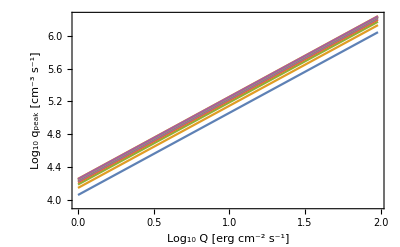

```mathematica
ListLinePlot[
Table[qtotmax[[;;,E0,{1,4}]],{E0,1,9,1}]
,Frame->True
,FrameLabel->{"Log_10 Q [erg cm^-2 s^-1]","Log_10 q_peak [cm^-3 s^-1]"}
]
```

```mathematica
Log10[50]//N
```

Log[50]/Log[10]